Integrals for Line charge problem.  θ = 0,π are special cases and are evaluated separately.

```mathematica
ClearAll[a,b,r,t]
$Assumptions =  t ∈ Reals && a ∈ Reals &&b ∈ Reals &&r >0 && b > a ;
i1 = Integrate[ (u^2 + 1 - 2 u Cos[t])^(-3/2), u]// FullSimplify
i2 = Integrate[ -u(u^2 + 1 - 2  u Cos[t])^(-3/2), u]// FullSimplify
i1z = Integrate[ (u^2 + 1 - 2 u )^(-3/2), u]//FullSimplify
i2z = Integrate[ -u(u^2 + 1 - 2  u )^(-3/2), u]// FullSimplify
i1pi = Integrate[ (u^2 + 1 + 2 u )^(-3/2), u]// FullSimplify
i2pi = Integrate[ -u(u^2 + 1 + 2  u )^(-3/2), u]// FullSimplify
```

((u-Cos[t]) Csc[t]^2)/(√(1+u^2-2 u Cos[t]))

(Csc[t] (-u Cot[t]+Csc[t]))/(√(1+u^2-2 u Cos[t]))

-(-1+u)/(2 ((-1+u)^2)^(3/2))

(√((-1+u)^2) (-1+2 u))/(2 (-1+u)^3)

-(1+u)/(2 ((1+u)^2)^(3/2))

(√((1+u)^2) (1+2 u))/(2 (1+u)^3)

```mathematica
int1[x_] := i1/. {t -> Pi/2,u->x};
int2[x_] := i2/. {t -> Pi/2,u->x};
```

```mathematica
int1[y]
int2[y]
int1[L/r]-int1[-L/r]
int2[L/r]-int2[-L/r]
```

y/(√(1+y^2))

1/(√(1+y^2))

(2 L)/(√(1+L^2/r^2) r)

0

```mathematica
1/Sin[x]
```

Csc[x]

```mathematica
<<peeters` ;
peeters`setGitDir[ "../project/figures/GAelectrodynamics" ]
```

/Users/pjoot/project/figures/GAelectrodynamics

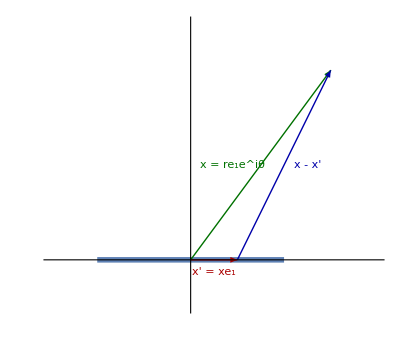

```mathematica
ClearAll[x,xp, o]
o = {0,0};
x = {3,4};
xp = {1,0};
e2 = {0,1};
e1 = {1,0};
bold = Style[ #, Bold] &;
sz = 14;
fs = Style[ #, FontSize-> sz] &;
tsub[t_,s_] := Subscript[bold[t]// fs,s];
esub := tsub[e, #]&;
vsub := tsub[v, #]&;
midpoint[p_] := (p[[1]] + p[[2]])/2 ;
midtext[p_, sh_,text_] := Text[text,midpoint[p] + sh]
p1 =Show[
ParametricPlot[{x,0}, {x,-2,2}, 
PlotStyle-> Thickness[0.01], GridLines -> Automatic,
Ticks->None,
PlotRange->{{-3,4}, {-1, 5}}
],
Graphics[ {
Green// Darker // Darker,
midtext[{o,x},-0.6 e1,Row[{ "x" // bold// fs, " = ", r// fs, esub[1], (e//fs)^("iθ" //fs)}]],
Arrow[{o,x}],
Red//Darker,
midtext[{o,xp},o-e2/4,
Row[{ "x'" // bold// fs, " = ", "x"// fs, esub[1]}]],
 Arrow[{o,xp}],
Blue // Darker,
 Arrow[{xp,x}],
midtext[{xp,x},0.5e1, Row[{ "x" // bold// fs, " - ", "x'" // bold// fs}]]
}]
]
```